```mathematica
ClearAll["Global`*"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Manipulate[Plot[nVKappa[pot,100,194,1.5,kappa],{pot,20,1000}],{kappa,1.501,5}]
```

```mathematica
kappaVals={1.6,2};
legs=Style[ToString[StringForm["κ = `1`",#]],Bold]&/@kappaVals
```

{κ = 1.6,κ = 2}

```mathematica
plotStyles={Blue,Orange};
```

NIntegrate::inumr: The integrand ((jvFuncs`Private`rho)^2 (Piecewise[{{1, Times[«2»]+Times[«2»]>0&&jvFuncs`Private`rho≥0}, {0, True}}]) Sin[jvFuncs`Private`theta])/((1+10. (-pot/194+(jvFuncs`Private`rho)^2))^2.6) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708},{0,30}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

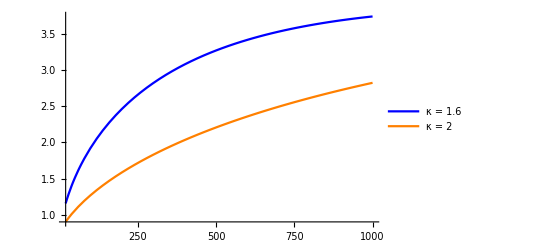

```mathematica
Plot[Evaluate@Table[nVKappaIntegrate[pot,100,194,1.5,kappa],{kappa,kappaVals}],{pot,20,1000},PlotLegends->legs,PlotStyle->plotStyles]
```